### PARAMETRES

```mathematica
listH ={100,100,100} (*мощности слоев*)
alpha = 0 Degree (*наклон слоев*)
len = 1000(*длина профиля*)
dx = 5(*шаг по профилю*)
anoMaxDisp = 100(*степень складчатости нижнего слоя в метрах*)
hTapering =5  (*степень влияния нижнего горизонта на верхние*)
listV = {1000,2000,3000, 4000} (*набор скоростей*)
numOfWells = 10 (*кол скважин*)
wellsLocation = "min" (*расположение скважин "max","min","regular","random"*)
type = 1 (*выполаживание. 1 - кверху, -1 - книзу!!!*)
```

{100,100,100}

0

1000

5

100

5

{1000,2000,3000,4000}

10

min

1

### DEPTH

```mathematica
horNH = BuildDepthSection[listH,alpha,len,dx,anoMaxDisp,hTapering, type][["horNH"]]
```

{{{0,22},{5,29},{10,36},{15,43},{20,49},{25,55},{30,60},{35,66},{40,71},{45,76},{50,80},{55,84},{60,87},{65,90},{70,93},{75,95},{80,97},{85,100},{90,102},{95,105},{100,108},{105,110},{110,112},{115,114},{120,115},{125,117},{130,118},{135,120},{140,123},{145,126},{150,128},{155,130},{160,132},{165,135},{170,136},{175,136},{180,137},{185,137},{190,138},{195,137},{200,137},{205,136},{210,137},{215,138},{220,136},{225,135},{230,134},{235,134},{240,132},{245,130},{250,130},{255,128},{260,127},{265,127},{270,128},{275,128},{280,127},{285,127},{290,127},{295,126},{300,127},{305,126},{310,127},{315,127},{320,127},{325,127},{330,128},{335,128},{340,129},{345,129},{350,129},{355,130},{360,131},{365,132},{370,132},{375,132},{380,133},{385,134},{390,134},{395,133},{400,132},{405,131},{410,131},{415,129},{420,127},{425,126},{430,125},{435,123},{440,121},{445,119},{450,116},{455,114},{460,111},{465,109},{470,106},{475,102},{480,99},{485,97},{490,95},{495,94},{500,92},{505,91},{510,90},{515,89},{520,89},{525,89},{530,89},{535,90},{540,92},{545,93},{550,95},{555,97},{560,99},{565,101},{570,102},{575,103},{580,106},{585,107},{590,106},{595,107},{600,108},{605,109},{610,109},{615,109},{620,108},{625,106},{630,105},{635,102},{640,100},{645,98},{650,95},{655,92},{660,88},{665,85},{670,82},{675,80},{680,78},{685,76},{690,76},{695,73},{700,71},{705,70},{710,68},{715,69},{720,69},{725,70},{730,71},{735,73},{740,74},{745,75},{750,77},{755,80},{760,81},{765,84},{770,87},{775,91},{780,95},{785,98},{790,101},{795,104},{800,106},{805,109},{810,111},{815,113},{820,115},{825,117},{830,119},{835,120},{840,122},{845,123},{850,124},{855,125},{860,125},{865,126},{870,125},{875,125},{880,124},{885,123},{890,123},{895,122},{900,122},{905,123},{910,122},{915,122},{920,122},{925,123},{930,123},{935,124},{940,125},{945,126},{950,127},{955,129},{960,130},{965,133},{970,136},{975,137},{980,139},{985,141},{990,144},{995,146},{1000,149}},{{0,-98},{5,-85},{10,-73},{15,-62},{20,-53},{25,-46},{30,-40},{35,-35},{40,-34},{45,-33},{50,-34},{55,-34},{60,-35},{65,-36},{70,-37},{75,-37},{80,-37},{85,-37},{90,-35},{95,-34},{100,-31},{105,-29},{110,-24},{115,-21},{120,-17},{125,-12},{130,-8},{135,-3},{140,0},{145,3},{150,6},{155,9},{160,11},{165,13},{170,14},{175,16},{180,18},{185,19},{190,19},{195,18},{200,19},{205,17},{210,14},{215,13},{220,10},{225,8},{230,6},{235,3},{240,0},{245,-2},{250,-2},{255,-5},{260,-7},{265,-8},{270,-9},{275,-9},{280,-10},{285,-8},{290,-6},{295,-5},{300,-3},{305,0},{310,1},{315,1},{320,2},{325,2},{330,3},{335,4},{340,4},{345,4},{350,4},{355,4},{360,2},{365,2},{370,1},{375,0},{380,0},{385,-1},{390,1},{395,2},{400,3},{405,5},{410,6},{415,8},{420,9},{425,11},{430,11},{435,10},{440,8},{445,6},{450,4},{455,0},{460,-6},{465,-12},{470,-20},{475,-27},{480,-35},{485,-43},{490,-48},{495,-52},{500,-57},{505,-59},{510,-61},{515,-62},{520,-61},{525,-59},{530,-55},{535,-50},{540,-44},{545,-38},{550,-34},{555,-30},{560,-26},{565,-22},{570,-17},{575,-14},{580,-12},{585,-11},{590,-8},{595,-7},{600,-7},{605,-7},{610,-7},{615,-7},{620,-9},{625,-13},{630,-15},{635,-18},{640,-21},{645,-25},{650,-29},{655,-33},{660,-39},{665,-44},{670,-49},{675,-55},{680,-58},{685,-62},{690,-65},{695,-67},{700,-68},{705,-71},{710,-72},{715,-72},{720,-72},{725,-72},{730,-70},{735,-69},{740,-66},{745,-63},{750,-59},{755,-57},{760,-51},{765,-46},{770,-42},{775,-36},{780,-32},{785,-27},{790,-22},{795,-19},{800,-16},{805,-13},{810,-10},{815,-7},{820,-4},{825,-3},{830,-2},{835,-2},{840,-2},{845,-1},{850,0},{855,0},{860,0},{865,1},{870,1},{875,0},{880,0},{885,-2},{890,-2},{895,-3},{900,-5},{905,-7},{910,-9},{915,-10},{920,-12},{925,-14},{930,-13},{935,-13},{940,-13},{945,-13},{950,-12},{955,-11},{960,-8},{965,-5},{970,-1},{975,3},{980,7},{985,11},{990,16},{995,20},{1000,25}},{{0,-212},{5,-194},{10,-178},{15,-164},{20,-153},{25,-146},{30,-141},{35,-141},{40,-143},{45,-146},{50,-149},{55,-153},{60,-158},{65,-161},{70,-163},{75,-162},{80,-164},{85,-162},{90,-159},{95,-156},{100,-152},{105,-149},{110,-144},{115,-139},{120,-135},{125,-130},{130,-126},{135,-121},{140,-116},{145,-113},{150,-109},{155,-108},{160,-105},{165,-102},{170,-102},{175,-101},{180,-101},{185,-99},{190,-98},{195,-98},{200,-98},{205,-99},{210,-101},{215,-101},{220,-104},{225,-107},{230,-111},{235,-114},{240,-118},{245,-123},{250,-127},{255,-131},{260,-132},{265,-132},{270,-133},{275,-132},{280,-130},{285,-127},{290,-125},{295,-124},{300,-120},{305,-118},{310,-117},{315,-115},{320,-114},{325,-113},{330,-114},{335,-114},{340,-114},{345,-115},{350,-113},{355,-114},{360,-114},{365,-116},{370,-118},{375,-119},{380,-119},{385,-122},{390,-123},{395,-121},{400,-119},{405,-119},{410,-116},{415,-112},{420,-109},{425,-108},{430,-104},{435,-99},{440,-97},{445,-99},{450,-103},{455,-110},{460,-116},{465,-124},{470,-134},{475,-145},{480,-155},{485,-166},{490,-175},{495,-184},{500,-191},{505,-193},{510,-193},{515,-192},{520,-188},{525,-184},{530,-176},{535,-171},{540,-165},{545,-158},{550,-150},{555,-140},{560,-136},{565,-134},{570,-131},{575,-129},{580,-129},{585,-128},{590,-126},{595,-125},{600,-124},{605,-123},{610,-125},{615,-125},{620,-125},{625,-126},{630,-127},{635,-128},{640,-132},{645,-138},{650,-145},{655,-152},{660,-161},{665,-166},{670,-172},{675,-178},{680,-182},{685,-185},{690,-188},{695,-189},{700,-191},{705,-191},{710,-192},{715,-191},{720,-192},{725,-192},{730,-192},{735,-193},{740,-190},{745,-188},{750,-186},{755,-180},{760,-174},{765,-167},{770,-161},{775,-154},{780,-146},{785,-142},{790,-135},{795,-132},{800,-129},{805,-125},{810,-125},{815,-125},{820,-124},{825,-123},{830,-122},{835,-121},{840,-119},{845,-120},{850,-119},{855,-117},{860,-118},{865,-115},{870,-116},{875,-114},{880,-116},{885,-118},{890,-119},{895,-121},{900,-123},{905,-126},{910,-128},{915,-129},{920,-131},{925,-133},{930,-135},{935,-137},{940,-138},{945,-137},{950,-135},{955,-132},{960,-130},{965,-128},{970,-125},{975,-119},{980,-114},{985,-108},{990,-102},{995,-96},{1000,-91}},{{0,-396},{5,-352},{10,-307},{15,-275},{20,-253},{25,-248},{30,-258},{35,-281},{40,-307},{45,-335},{50,-355},{55,-367},{60,-368},{65,-361},{70,-346},{75,-332},{80,-322},{85,-317},{90,-316},{95,-320},{100,-326},{105,-335},{110,-339},{115,-334},{120,-327},{125,-314},{130,-298},{135,-279},{140,-264},{145,-258},{150,-259},{155,-268},{160,-276},{165,-286},{170,-292},{175,-289},{180,-285},{185,-274},{190,-263},{195,-256},{200,-253},{205,-257},{210,-264},{215,-273},{220,-279},{225,-283},{230,-284},{235,-283},{240,-282},{245,-287},{250,-296},{255,-308},{260,-318},{265,-324},{270,-328},{275,-326},{280,-320},{285,-310},{290,-295},{295,-286},{300,-275},{305,-266},{310,-264},{315,-270},{320,-286},{325,-296},{330,-306},{335,-310},{340,-307},{345,-295},{350,-278},{355,-269},{360,-263},{365,-264},{370,-273},{375,-287},{380,-307},{385,-314},{390,-314},{395,-308},{400,-303},{405,-296},{410,-293},{415,-292},{420,-289},{425,-283},{430,-275},{435,-261},{440,-250},{445,-241},{450,-244},{455,-252},{460,-267},{465,-281},{470,-300},{475,-317},{480,-332},{485,-348},{490,-368},{495,-386},{500,-397},{505,-395},{510,-388},{515,-380},{520,-374},{525,-366},{530,-357},{535,-350},{540,-339},{545,-321},{550,-302},{555,-288},{560,-287},{565,-292},{570,-302},{575,-311},{580,-311},{585,-308},{590,-297},{595,-284},{600,-281},{605,-289},{610,-300},{615,-311},{620,-318},{625,-314},{630,-297},{635,-284},{640,-270},{645,-269},{650,-281},{655,-301},{660,-326},{665,-356},{670,-377},{675,-389},{680,-393},{685,-391},{690,-380},{695,-366},{700,-352},{705,-340},{710,-336},{715,-338},{720,-345},{725,-361},{730,-375},{735,-386},{740,-395},{745,-396},{750,-390},{755,-376},{760,-358},{765,-334},{770,-316},{775,-304},{780,-293},{785,-294},{790,-295},{795,-302},{800,-305},{805,-304},{810,-304},{815,-299},{820,-297},{825,-291},{830,-285},{835,-286},{840,-289},{845,-294},{850,-298},{855,-304},{860,-303},{865,-293},{870,-282},{875,-270},{880,-266},{885,-273},{890,-283},{895,-297},{900,-305},{905,-307},{910,-306},{915,-304},{920,-305},{925,-308},{930,-311},{935,-312},{940,-310},{945,-311},{950,-307},{955,-309},{960,-311},{965,-312},{970,-311},{975,-307},{980,-298},{985,-286},{990,-273},{995,-259},{1000,-248}}}

```mathematica
PlotDepthSection[horNH, Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horNH]] - 1)],
						PlotLabel -> "Depth Section"]
```

-Graphics-

### VELOCITY

```mathematica
velModel=BuildVelocitySection[horNH,listV][["velModel"]]
datasetVelModel=BuildVelocitySection[horNH,listV][["datasetVelModel"]]
```

Dataset[<>]

```mathematica
PlotVelocity[velModel, horNH, {PlotStyle -> {Directive[Thickness[0.005], Black]},
							PlotLabel->"Velocity Distribution",
							PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horNH]] - 1)],
							ImageSize -> 500, 
ColorFunction -> ColorData[{"RedBlueTones", "Reverse"}],
						PlotLegends -> BarLegend[Automatic, LegendLabel -> "Vel, m/s"],
						PlotLabel -> "Velocity Distribution",
						Contours -> {Automatic, 10}}]
```

-Graphics-

### TIME

```mathematica
timeNH=BuildTimeSection[horNH, velModel][["timeNH"]]
```

{{{0,0},{5,0},{10,0},{15,0},{20,0},{25,0},{30,0},{35,0},{40,0},{45,0},{50,0},{55,0},{60,0},{65,0},{70,0},{75,0},{80,0},{85,0},{90,0},{95,0},{100,0},{105,0},{110,0},{115,0},{120,0},{125,0},{130,0},{135,0},{140,0},{145,0},{150,0},{155,0},{160,0},{165,0},{170,0},{175,0},{180,0},{185,0},{190,0},{195,0},{200,0},{205,0},{210,0},{215,0},{220,0},{225,0},{230,0},{235,0},{240,0},{245,0},{250,0},{255,0},{260,0},{265,0},{270,0},{275,0},{280,0},{285,0},{290,0},{295,0},{300,0},{305,0},{310,0},{315,0},{320,0},{325,0},{330,0},{335,0},{340,0},{345,0},{350,0},{355,0},{360,0},{365,0},{370,0},{375,0},{380,0},{385,0},{390,0},{395,0},{400,0},{405,0},{410,0},{415,0},{420,0},{425,0},{430,0},{435,0},{440,0},{445,0},{450,0},{455,0},{460,0},{465,0},{470,0},{475,0},{480,0},{485,0},{490,0},{495,0},{500,0},{505,0},{510,0},{515,0},{520,0},{525,0},{530,0},{535,0},{540,0},{545,0},{550,0},{555,0},{560,0},{565,0},{570,0},{575,0},{580,0},{585,0},{590,0},{595,0},{600,0},{605,0},{610,0},{615,0},{620,0},{625,0},{630,0},{635,0},{640,0},{645,0},{650,0},{655,0},{660,0},{665,0},{670,0},{675,0},{680,0},{685,0},{690,0},{695,0},{700,0},{705,0},{710,0},{715,0},{720,0},{725,0},{730,0},{735,0},{740,0},{745,0},{750,0},{755,0},{760,0},{765,0},{770,0},{775,0},{780,0},{785,0},{790,0},{795,0},{800,0},{805,0},{810,0},{815,0},{820,0},{825,0},{830,0},{835,0},{840,0},{845,0},{850,0},{855,0},{860,0},{865,0},{870,0},{875,0},{880,0},{885,0},{890,0},{895,0},{900,0},{905,0},{910,0},{915,0},{920,0},{925,0},{930,0},{935,0},{940,0},{945,0},{950,0},{955,0},{960,0},{965,0},{970,0},{975,0},{980,0},{985,0},{990,0},{995,0},{1000,0}},{{0,0.0978198},{5,0.097062},{10,0.0969666},{15,0.0975166},{20,0.0983971},{25,0.100437},{30,0.102066},{35,0.105254},{40,0.109709},{45,0.114052},{50,0.118583},{55,0.1225},{60,0.125892},{65,0.129284},{70,0.132716},{75,0.134677},{80,0.136487},{85,0.139418},{90,0.140222},{95,0.142516},{100,0.143731},{105,0.144547},{110,0.143702},{115,0.144001},{120,0.142847},{125,0.142128},{130,0.140943},{135,0.140306},{140,0.141485},{145,0.147243},{150,0.152038},{155,0.156801},{160,0.16058},{165,0.165167},{170,0.16706},{175,0.16914},{180,0.171958},{185,0.172943},{190,0.173945},{195,0.172042},{200,0.173074},{205,0.170164},{210,0.168009},{215,0.16783},{220,0.16314},{225,0.160152},{230,0.157384},{235,0.154388},{240,0.149595},{245,0.148802},{250,0.148855},{255,0.148471},{260,0.148509},{265,0.149113},{270,0.150445},{275,0.150463},{280,0.150186},{285,0.14911},{290,0.148152},{295,0.146696},{300,0.146614},{305,0.144362},{310,0.146177},{315,0.146112},{320,0.147123},{325,0.147087},{330,0.148938},{335,0.149942},{340,0.150884},{345,0.150929},{350,0.150879},{355,0.15174},{360,0.150651},{365,0.151671},{370,0.150627},{375,0.149609},{380,0.150544},{385,0.151922},{390,0.152346},{395,0.152428},{400,0.152536},{405,0.153644},{410,0.154685},{415,0.154841},{420,0.154021},{425,0.155216},{430,0.154334},{435,0.151554},{440,0.147693},{445,0.143894},{450,0.139213},{455,0.133299},{460,0.133584},{465,0.134773},{470,0.136171},{475,0.136023},{480,0.137507},{485,0.13992},{490,0.140711},{495,0.141884},{500,0.142652},{505,0.142854},{510,0.143126},{515,0.142876},{520,0.142438},{525,0.141381},{530,0.139262},{535,0.137299},{540,0.135819},{545,0.133484},{550,0.133273},{555,0.133108},{560,0.132794},{565,0.132409},{570,0.130769},{575,0.130085},{580,0.131928},{585,0.132375},{590,0.12988},{595,0.130202},{600,0.131279},{605,0.132218},{610,0.132163},{615,0.132204},{620,0.132252},{625,0.132433},{630,0.132556},{635,0.131436},{640,0.131034},{645,0.131273},{650,0.1305},{655,0.129751},{660,0.1291},{665,0.128996},{670,0.128912},{675,0.130371},{680,0.130195},{685,0.130577},{690,0.132426},{695,0.130647},{700,0.129213},{705,0.130252},{710,0.128854},{715,0.129912},{720,0.129876},{725,0.130813},{730,0.130499},{735,0.131774},{740,0.131022},{745,0.130179},{750,0.129642},{755,0.131561},{760,0.129063},{765,0.12925},{770,0.129931},{775,0.130437},{780,0.132185},{785,0.132332},{790,0.132497},{795,0.133698},{800,0.134141},{805,0.135277},{810,0.135493},{815,0.135866},{820,0.136164},{825,0.137573},{830,0.138869},{835,0.139841},{840,0.141655},{845,0.141993},{850,0.142459},{855,0.143366},{860,0.143342},{865,0.145236},{870,0.144262},{875,0.143352},{880,0.142468},{885,0.14249},{890,0.142571},{895,0.14218},{900,0.143081},{905,0.145003},{910,0.145225},{915,0.145555},{920,0.146703},{925,0.148557},{930,0.148069},{935,0.148936},{940,0.14979},{945,0.15074},{950,0.151105},{955,0.152418},{960,0.15168},{965,0.152997},{970,0.153628},{975,0.156972},{980,0.162678},{985,0.168497},{990,0.176098},{995,0.18188},{1000,0.189676}},{{0,0.206437},{5,0.198147},{10,0.19176},{15,0.186147},{20,0.181919},{25,0.179964},{30,0.177858},{35,0.179716},{40,0.183926},{45,0.18863},{50,0.193951},{55,0.199519},{60,0.205534},{65,0.210972},{70,0.216285},{75,0.218482},{80,0.221959},{85,0.224086},{90,0.223174},{95,0.223509},{100,0.222117},{105,0.220733},{110,0.216946},{115,0.21473},{120,0.211684},{125,0.208729},{130,0.205985},{135,0.203342},{140,0.202391},{145,0.206716},{150,0.209192},{155,0.213025},{160,0.214817},{165,0.217431},{170,0.219126},{175,0.220743},{180,0.22371},{185,0.223952},{190,0.22479},{195,0.223149},{200,0.224219},{205,0.221751},{210,0.220497},{215,0.219991},{220,0.21673},{225,0.215256},{230,0.21465},{235,0.213429},{240,0.210893},{245,0.212664},{250,0.214574},{255,0.215892},{260,0.216073},{265,0.216398},{270,0.218118},{275,0.217664},{280,0.216563},{285,0.214224},{290,0.212784},{295,0.21116},{300,0.209328},{305,0.206287},{310,0.207613},{315,0.206196},{320,0.205961},{325,0.204995},{330,0.207082},{335,0.207927},{340,0.208975},{345,0.20998},{350,0.20953},{355,0.211279},{360,0.210473},{365,0.212581},{370,0.212301},{375,0.211255},{380,0.211366},{385,0.214127},{390,0.215105},{395,0.214317},{400,0.213512},{405,0.214869},{410,0.214391},{415,0.212385},{420,0.21001},{425,0.21085},{430,0.208066},{435,0.203005},{440,0.198446},{445,0.196116},{450,0.193581},{455,0.191296},{460,0.194367},{465,0.199417},{470,0.205626},{475,0.210859},{480,0.217246},{485,0.225051},{490,0.229903},{495,0.235162},{500,0.239172},{505,0.240682},{510,0.241288},{515,0.241002},{520,0.238692},{525,0.235739},{530,0.229618},{535,0.225237},{540,0.220931},{545,0.215578},{550,0.211766},{555,0.206615},{560,0.204052},{565,0.202281},{570,0.19846},{575,0.19629},{580,0.198137},{585,0.198152},{590,0.194981},{595,0.1953},{600,0.195963},{605,0.195997},{610,0.196589},{615,0.196217},{620,0.195937},{625,0.19685},{630,0.198219},{635,0.19827},{640,0.200898},{645,0.204578},{650,0.207298},{655,0.209511},{660,0.212645},{665,0.213711},{670,0.215915},{675,0.220108},{680,0.22196},{685,0.224147},{690,0.228291},{695,0.227946},{700,0.228601},{705,0.23054},{710,0.229876},{715,0.230213},{720,0.230265},{725,0.230188},{730,0.228969},{735,0.230088},{740,0.227107},{745,0.225057},{750,0.223788},{755,0.223076},{760,0.21824},{765,0.215799},{770,0.214064},{775,0.211123},{780,0.208887},{785,0.206669},{790,0.202762},{795,0.201976},{800,0.200569},{805,0.199547},{810,0.199732},{815,0.200373},{820,0.200163},{825,0.201272},{830,0.202243},{835,0.202624},{840,0.203192},{845,0.20387},{850,0.203627},{855,0.203173},{860,0.203782},{865,0.20437},{870,0.204396},{875,0.202886},{880,0.203303},{885,0.204141},{890,0.204373},{895,0.204494},{900,0.206203},{905,0.209709},{910,0.21108},{915,0.212017},{920,0.214253},{925,0.217109},{930,0.217622},{935,0.219557},{940,0.221049},{945,0.221372},{950,0.220821},{955,0.220341},{960,0.218433},{965,0.218583},{970,0.217614},{975,0.217831},{980,0.221085},{985,0.224057},{990,0.228796},{995,0.231728},{1000,0.237169}},{{0,0.399938},{5,0.35649},{10,0.324205},{15,0.302236},{20,0.287261},{25,0.282926},{30,0.285606},{35,0.298794},{40,0.316462},{45,0.336652},{50,0.354049},{55,0.367661},{60,0.374418},{65,0.375022},{70,0.37095},{75,0.364885},{80,0.362491},{85,0.36201},{90,0.360569},{95,0.362994},{100,0.364896},{105,0.36875},{110,0.367291},{115,0.362217},{120,0.35514},{125,0.344922},{130,0.333853},{135,0.321428},{140,0.31309},{145,0.314494},{150,0.317526},{155,0.325716},{160,0.33149},{165,0.338972},{170,0.343751},{175,0.343832},{180,0.344856},{185,0.339628},{190,0.334988},{195,0.329944},{200,0.329725},{205,0.329106},{210,0.331245},{215,0.335012},{220,0.334733},{225,0.3353},{230,0.335202},{235,0.333507},{240,0.330562},{245,0.334803},{250,0.3413},{255,0.34897},{260,0.354418},{265,0.357979},{270,0.362238},{275,0.360468},{280,0.355991},{285,0.348299},{290,0.338926},{295,0.332834},{300,0.325445},{305,0.317986},{310,0.318381},{315,0.319821},{320,0.327635},{325,0.331775},{330,0.339065},{335,0.342064},{340,0.341391},{345,0.336149},{350,0.327096},{355,0.324512},{360,0.320734},{365,0.323271},{370,0.327497},{375,0.333401},{380,0.343868},{385,0.3505},{390,0.351359},{395,0.347322},{400,0.343941},{405,0.341658},{410,0.339559},{415,0.337059},{420,0.333087},{425,0.330814},{430,0.324211},{435,0.312289},{440,0.302425},{445,0.295827},{450,0.2947},{455,0.29617},{460,0.306549},{465,0.318542},{470,0.334462},{475,0.348777},{480,0.363506},{485,0.380857},{490,0.398614},{495,0.418114},{500,0.434907},{505,0.433955},{510,0.426014},{515,0.419219},{520,0.411528},{525,0.402864},{530,0.391002},{535,0.382244},{540,0.371133},{545,0.355708},{550,0.341557},{555,0.329271},{560,0.32613},{565,0.327016},{570,0.328246},{575,0.330888},{580,0.332826},{585,0.331222},{590,0.322196},{595,0.315863},{600,0.315048},{605,0.319051},{610,0.325422},{615,0.330855},{620,0.334427},{625,0.333106},{630,0.325387},{635,0.318804},{640,0.314478},{645,0.317671},{650,0.326303},{655,0.338736},{660,0.355433},{665,0.374626},{670,0.391145},{675,0.405633},{680,0.411388},{685,0.412004},{690,0.406078},{695,0.395646},{700,0.386896},{705,0.381414},{710,0.37819},{715,0.379759},{720,0.384148},{725,0.394075},{730,0.403145},{735,0.412475},{740,0.420521},{745,0.418448},{750,0.410574},{755,0.397512},{760,0.380234},{765,0.363153},{770,0.351369},{775,0.342047},{780,0.334079},{785,0.332401},{790,0.329008},{795,0.331777},{800,0.331922},{805,0.330453},{810,0.330698},{815,0.328637},{820,0.327298},{825,0.325473},{830,0.323438},{835,0.324254},{840,0.326331},{845,0.329501},{850,0.331423},{855,0.334076},{860,0.334067},{865,0.329482},{870,0.323928},{875,0.316505},{880,0.314992},{885,0.319291},{890,0.324396},{895,0.331766},{900,0.337573},{905,0.342197},{910,0.342964},{915,0.342892},{920,0.345577},{925,0.350056},{930,0.35212},{935,0.354866},{940,0.355049},{945,0.355983},{950,0.353229},{955,0.353966},{960,0.353087},{965,0.353713},{970,0.352253},{975,0.350477},{980,0.348852},{985,0.345596},{990,0.343944},{995,0.339967},{1000,0.340185}}}

```mathematica
PlotTimeSection[timeNH, {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[timeNH]] - 1)],
						PlotLabel -> "Time Section"}]
```

-Graphics-

### WELLS

```mathematica
datasetWells=BuildWellSet[horNH,timeNH, numOfWells, wellsLocation][["datasetWells"]]
```

```mathematica
PlotDepthSection[horNH, datasetWells,{GridLines->{DeleteDuplicates[Normal[datasetWells[All, "x"]]], None},
											Filling -> Bottom, Frame -> True, ImageSize -> 500,
											PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horNH]] - 1)],
											PlotLabel -> "Depth Section with wells"}]
```

-Graphics-

```mathematica
PlotTimeSection[timeNH, {GridLines->{DeleteDuplicates[Normal[datasetWells[All, "x"]]], None},
					    Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[timeNH]] - 1)],
						PlotLabel -> "Time Section with Wells"
}]
```

-Graphics-

### Vint

```mathematica
listVint = CheckVelocity[datasetWells][["datasetVint"]]
```

### HT

```mathematica
Clear[t]

dataWellsHT=HT[datasetWells,timeNH, t][["dataWellsHT"]]
lmSetHT=HT[datasetWells,timeNH, t][["lmSet"]]
fitsHTParams=HT[datasetWells, timeNH, t][["fitsHTParams"]]
resultHT=HT[datasetWells, timeNH, t][["resultHT"]]
```

{{{0.143702,-24.},{0.150445,-9.},{0.151922,-1.},{0.142652,-57.},{0.130085,-14.},{0.132252,-9.},{0.130195,-58.},{0.134141,-16.},{0.143366,0.},{0.148936,-13.}},{{0.216946,-144.},{0.218118,-133.},{0.214127,-122.},{0.239172,-191.},{0.19629,-129.},{0.195937,-125.},{0.22196,-182.},{0.200569,-129.},{0.203173,-117.},{0.219557,-137.}},{{0.367291,-339.},{0.362238,-328.},{0.3505,-314.},{0.434907,-397.},{0.330888,-311.},{0.334427,-318.},{0.411388,-393.},{0.331922,-305.},{0.334076,-304.},{0.354866,-312.}}}

{FittedModel[-142.902+872.363 t],FittedModel[171.722-1470.57 t],FittedModel[10.0477-947.121 t]}

{{-142.902,872.363},{171.722,-1470.57},{10.0477,-947.121}}

{{{110,112.},{270,128.},{385,134.},{500,92.},{575,103.},{620,108.},{680,78.},{800,106.},{855,125.},{935,124.}},{{0,132.197},{5,116.575},{10,102.195},{15,89.0291},{20,76.7884},{25,66.183},{30,55.8305},{35,47.4345},{40,40.7284},{45,34.4963},{50,28.9853},{55,23.4826},{60,18.0535},{65,13.1421},{70,8.77071},{75,3.6067},{80,-1.21081},{85,-4.58615},{90,-9.36465},{95,-12.4051},{100,-15.9625},{105,-19.4562},{110,-24.},{115,-27.1609},{120,-31.2179},{125,-34.5357},{130,-37.9162},{135,-40.4853},{140,-41.1523},{145,-37.519},{150,-34.4331},{155,-31.0965},{160,-28.3527},{165,-24.6521},{170,-23.0619},{175,-21.0823},{180,-18.2472},{185,-16.8113},{190,-15.1743},{195,-15.8988},{200,-13.904},{205,-15.2014},{210,-15.7069},{215,-14.3693},{220,-16.8612},{225,-17.7739},{230,-18.4156},{235,-19.1896},{240,-21.4775},{245,-20.2356},{250,-18.2298},{255,-16.5908},{260,-14.5842},{265,-12.0959},{270,-9.},{275,-7.08916},{280,-5.489},{285,-4.65113},{290,-3.79081},{295,-3.45701},{300,-2.03048},{305,-2.61616},{310,0.214097},{315,1.25729},{320,3.08112},{325,3.81893},{330,6.01738},{335,7.27873},{340,8.27261},{345,8.25954},{350,7.92471},{355,8.13272},{360,6.37425},{365,6.17747},{370,3.88805},{375,1.31677},{380,0.130786},{385,-1.},{390,-3.29775},{395,-6.18952},{400,-9.30217},{405,-11.7383},{410,-14.3778},{415,-17.8849},{420,-22.2882},{425,-24.9287},{430,-29.3268},{435,-35.2766},{440,-42.0148},{445,-48.4948},{450,-55.4898},{455,-63.2558},{460,-65.2596},{465,-66.0712},{470,-66.2468},{475,-67.2675},{480,-66.3099},{485,-63.9379},{490,-62.3332},{495,-59.77},{500,-57.},{505,-54.2281},{510,-50.9679},{515,-47.8},{520,-44.4999},{525,-41.5083},{530,-39.2794},{535,-36.8155},{540,-33.8977},{545,-31.7583},{550,-27.8664},{555,-24.0986},{560,-20.6924},{565,-17.6448},{570,-16.0478},{575,-14.},{580,-10.1529},{585,-7.94882},{590,-8.7567},{595,-7.57433},{600,-6.21972},{605,-5.4944},{610,-6.16424},{615,-7.29994},{620,-9.},{625,-11.174},{630,-13.9915},{635,-18.4097},{640,-22.6229},{645,-26.6023},{650,-31.6968},{655,-36.9049},{660,-42.0686},{665,-46.7011},{670,-51.1653},{675,-54.04},{680,-58.},{685,-61.0388},{690,-62.2679},{695,-66.0363},{700,-68.7825},{705,-68.5838},{710,-69.7661},{715,-68.1304},{720,-66.844},{725,-64.1734},{730,-62.1301},{735,-58.3071},{740,-55.9277},{745,-53.3735},{750,-50.3692},{755,-45.1095},{760,-43.6592},{765,-39.8944},{770,-35.7951},{775,-32.0167},{780,-27.3918},{785,-24.4412},{790,-21.7482},{795,-18.4164},{800,-16.},{805,-13.2271},{810,-11.4941},{815,-9.85384},{820,-8.49891},{825,-6.38788},{830,-4.57768},{835,-3.24515},{840,-1.36336},{845,-0.946143},{850,-0.585116},{855,3.55271×10^-15},{860,-0.376764},{865,0.776779},{870,-0.704678},{875,-2.25448},{880,-3.89785},{885,-4.85788},{890,-5.86498},{895,-7.37345},{900,-7.8357},{905,-7.4796},{910,-8.66995},{915,-9.82045},{920,-10.3041},{925,-10.209},{930,-12.1855},{935,-13.},{940,-13.8367},{945,-14.5921},{950,-15.8513},{955,-16.2682},{960,-18.4516},{965,-18.8091},{970,-19.724},{975,-18.2214},{980,-14.6001},{985,-10.8136},{990,-5.39525},{995,-1.47889}},{{0,-65.6966},{5,-58.544},{10,-53.9508},{15,-50.2591},{20,-48.3726},{25,-49.6033},{30,-50.391},{35,-56.7929},{40,-66.4405},{45,-76.6093},{50,-87.4849},{55,-98.527},{60,-110.034},{65,-120.506},{70,-130.615},{75,-135.963},{80,-143.023},{85,-147.929},{90,-148.206},{95,-150.16},{100,-149.422},{105,-148.549},{110,-144.},{115,-141.624},{120,-137.895},{125,-134.174},{130,-130.641},{135,-127.139},{140,-126.012},{145,-132.538},{150,-136.242},{155,-141.843},{160,-144.351},{165,-147.98},{170,-150.175},{175,-152.177},{180,-156.093},{185,-155.932},{190,-156.587},{195,-153.537},{200,-154.421},{205,-150.054},{210,-147.428},{215,-145.865},{220,-140.218},{225,-137.169},{230,-135.374},{235,-132.657},{240,-127.992},{245,-129.653},{250,-131.515},{255,-132.507},{260,-131.833},{265,-131.382},{270,-133.},{275,-131.44},{280,-128.957},{285,-124.683},{290,-121.768},{295,-118.623},{300,-115.218},{305,-110.086},{310,-111.431},{315,-108.804},{320,-107.98},{325,-106.152},{330,-108.89},{335,-109.881},{340,-111.257},{345,-112.659},{350,-112.017},{355,-114.709},{360,-113.748},{365,-117.184},{370,-117.223},{375,-116.256},{380,-117.114},{385,-122.},{390,-124.395},{395,-124.318},{400,-124.326},{405,-127.612},{410,-128.288},{415,-126.791},{420,-124.817},{425,-127.622},{430,-125.137},{435,-119.332},{440,-114.281},{445,-112.514},{450,-110.436},{455,-108.707},{460,-114.823},{465,-123.806},{470,-134.44},{475,-143.569},{480,-154.318},{485,-167.063},{490,-175.362},{495,-184.153},{500,-191.},{505,-194.064},{510,-195.688},{515,-195.892},{520,-193.01},{525,-189.073},{530,-180.367},{535,-174.109},{540,-167.849},{545,-159.937},{550,-154.179},{555,-146.339},{560,-142.19},{565,-139.093},{570,-132.871},{575,-129.},{580,-130.995},{585,-130.294},{590,-124.942},{595,-124.792},{600,-125.256},{605,-124.94},{610,-125.628},{615,-125.118},{620,-125.},{625,-126.93},{630,-129.847},{635,-131.112},{640,-136.407},{645,-143.444},{650,-149.217},{655,-154.348},{660,-160.892},{665,-164.408},{670,-169.563},{675,-177.565},{680,-182.},{685,-186.758},{690,-194.179},{695,-194.737},{700,-196.46},{705,-199.731},{710,-198.847},{715,-199.132},{720,-198.72},{725,-197.863},{730,-195.098},{735,-195.565},{740,-189.823},{745,-185.293},{750,-181.779},{755,-178.978},{760,-170.03},{765,-164.543},{770,-160.061},{775,-153.797},{780,-148.584},{785,-143.427},{790,-135.822},{795,-132.846},{800,-129.},{805,-125.763},{810,-124.352},{815,-123.663},{820,-121.778},{825,-121.891},{830,-121.863},{835,-121.032},{840,-120.546},{845,-120.293},{850,-118.763},{855,-117.},{860,-116.882},{865,-116.82},{870,-116.019},{875,-113.051},{880,-113.013},{885,-113.692},{890,-113.582},{895,-113.415},{900,-115.692},{905,-120.723},{910,-122.731},{915,-124.219},{920,-127.739},{925,-132.296},{930,-133.537},{935,-137.},{940,-139.949},{945,-141.315},{950,-141.539},{955,-142.014},{960,-140.537},{965,-142.238},{970,-142.45},{975,-144.563},{980,-151.306},{985,-157.8},{990,-167.06},{995,-173.834}},{{0,-380.85},{5,-339.022},{10,-307.786},{15,-286.34},{20,-271.536},{25,-266.829},{30,-268.784},{35,-280.71},{40,-296.895},{45,-315.486},{50,-331.448},{55,-343.843},{60,-349.76},{65,-349.867},{70,-345.559},{75,-339.379},{80,-336.691},{85,-335.828},{90,-334.07},{95,-335.988},{100,-337.424},{105,-340.722},{110,-339.},{115,-333.867},{120,-326.848},{125,-316.867},{130,-306.091},{135,-294.04},{140,-285.873},{145,-286.941},{150,-289.563},{155,-297.078},{160,-302.315},{165,-309.178},{170,-313.491},{175,-313.361},{180,-314.134},{185,-308.992},{190,-304.414},{195,-299.459},{200,-299.082},{205,-298.333},{210,-300.201},{215,-303.617},{220,-303.206},{225,-303.6},{230,-303.37},{235,-301.631},{240,-298.713},{245,-302.604},{250,-308.635},{255,-315.78},{260,-320.822},{265,-324.08},{270,-328.},{275,-326.212},{280,-321.861},{285,-314.466},{290,-305.479},{295,-299.6},{300,-292.492},{305,-285.318},{310,-285.581},{315,-286.832},{320,-294.12},{325,-297.924},{330,-304.711},{335,-307.431},{340,-306.671},{345,-301.579},{350,-292.875},{355,-290.293},{360,-286.577},{365,-288.836},{370,-292.691},{375,-298.129},{380,-307.884},{385,-314.},{390,-314.644},{395,-310.647},{400,-307.275},{405,-304.949},{410,-302.807},{415,-300.301},{420,-296.42},{425,-294.172},{430,-287.851},{435,-276.523},{440,-267.182},{445,-260.973},{450,-259.992},{455,-261.519},{460,-271.538},{465,-283.142},{470,-298.528},{475,-312.46},{480,-326.854},{485,-343.805},{490,-361.22},{495,-380.359},{500,-397.},{505,-396.889},{510,-390.205},{515,-384.643},{520,-378.261},{525,-370.976},{530,-360.67},{535,-353.305},{540,-343.7},{545,-329.993},{550,-317.463},{555,-306.663},{560,-304.477},{565,-306.05},{570,-307.886},{575,-311.},{580,-313.392},{585,-312.38},{590,-304.293},{595,-298.717},{600,-298.333},{605,-302.484},{610,-308.853},{615,-314.315},{620,-318.},{625,-317.042},{630,-310.02},{635,-304.065},{640,-300.232},{645,-303.503},{650,-311.899},{655,-323.866},{660,-339.836},{665,-358.131},{670,-373.846},{675,-387.587},{680,-393.},{685,-393.484},{690,-387.706},{695,-377.588},{700,-368.986},{705,-363.399},{710,-359.876},{715,-360.828},{720,-364.396},{725,-373.161},{730,-381.077},{735,-389.21},{740,-396.108},{745,-393.409},{750,-385.216},{755,-372.113},{760,-355.035},{765,-338.167},{770,-326.35},{775,-316.906},{780,-308.796},{785,-306.699},{790,-303.028},{795,-305.237},{800,-305.},{805,-303.269},{810,-303.19},{815,-300.95},{820,-299.412},{825,-297.427},{830,-295.25},{835,-295.775},{840,-297.491},{845,-300.234},{850,-301.781},{855,-304.},{860,-303.673},{865,-298.984},{870,-293.34},{875,-285.885},{880,-283.982},{885,-287.532},{890,-291.788},{895,-298.127},{900,-302.919},{905,-306.517},{910,-306.384},{915,-305.373},{920,-306.885},{925,-310.001},{930,-310.73},{935,-312.},{940,-310.732},{945,-310.06},{950,-305.774},{955,-304.668},{960,-301.9},{965,-300.42},{970,-296.822},{975,-292.778},{980,-288.723},{985,-282.964},{990,-278.562},{995,-271.787}}}

Missing[KeyAbsent,wellsSet]

Missing[KeyAbsent,htSet]

Missing[KeyAbsent,interpolationErrors]

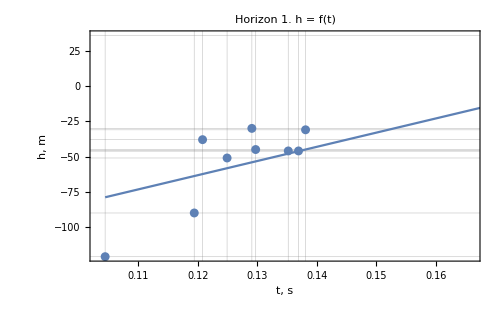
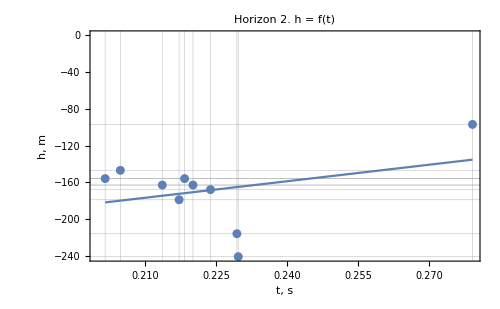
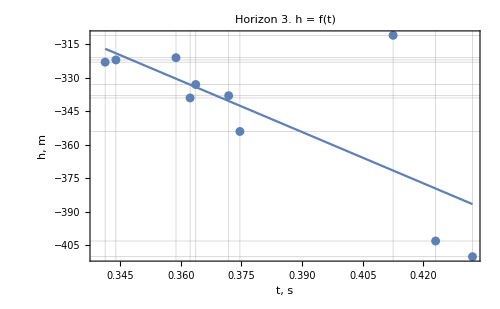

```mathematica
PlotHT[dataWellsHT,lmSetHT, t]
```

### VT

```mathematica
Clear[t]
lmSetVT=VT[datasetWells,datasetVelModel,timeNH, t][["lmSet"]]
setVT=VT[datasetWells,datasetVelModel,timeNH, t][["setVT"]]
fitParamsVT=VT[datasetWells,datasetVelModel,timeNH, t][["fitParams"]]
```

{FittedModel[1949.94+344.962 t],FittedModel[2996.37-5.01722 t],FittedModel[4054.6-159.732 t]}

{{{1,0.143702,1987},{1,0.150445,2011},{1,0.151922,2003},{1,0.142652,1983},{1,0.130085,2011},{1,0.132252,2006},{1,0.130195,1988},{1,0.134141,1985},{1,0.143366,1999},{1,0.148936,2012}},{{2,0.216946,2988},{2,0.218118,2994},{2,0.214127,2994},{2,0.239172,3030},{2,0.19629,3021},{2,0.195937,3011},{2,0.22196,2970},{2,0.200569,2986},{2,0.203173,2987},{2,0.219557,2972}},{{3,0.367291,3994},{3,0.362238,3990},{3,0.3505,3995},{3,0.434907,3979},{3,0.330888,4037},{3,0.334427,3988},{3,0.411388,3992},{3,0.331922,3984},{3,0.334076,3975},{3,0.354866,4035}}}

{{1949.94,344.962},{2996.37,-5.01722},{4054.6,-159.732}}

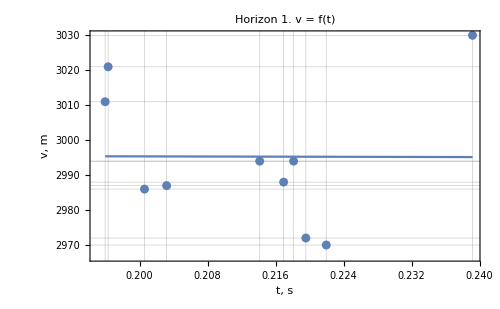
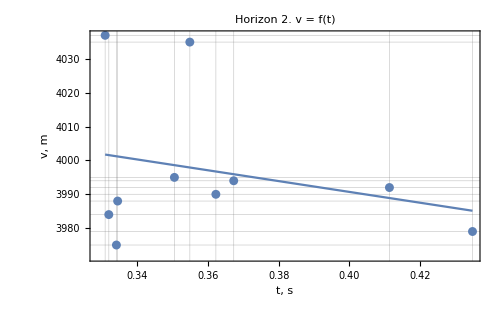

```mathematica
PlotVT[setVT,lmSetVT, t]
```

### Graphics

```mathematica
resultVT = VT[datasetWells,datasetVelModel,timeNH, t][["resultVT"]]
```

{{{110,112.},{270,128.},{385,134.},{500,92.},{575,103.},{620,108.},{680,78.},{800,106.},{855,125.},{935,124.}},{{0,183.778},{5,169.8},{10,156.149},{15,142.819},{20,129.954},{25,117.128},{30,105.107},{35,92.9003},{40,80.6386},{45,68.9924},{50,57.8001},{55,47.4476},{60,37.8774},{65,28.8154},{70,20.228},{75,12.8567},{80,6.02978},{85,-0.900926},{90,-6.32719},{95,-12.0685},{100,-16.854},{105,-21.037},{110,-24.},{115,-27.1581},{120,-29.2261},{125,-31.1621},{130,-32.5274},{135,-33.8435},{140,-35.7559},{145,-39.6607},{150,-42.8024},{155,-45.659},{160,-47.7666},{165,-50.0361},{170,-50.7243},{175,-51.2889},{180,-52.0194},{185,-51.6384},{190,-51.0879},{195,-48.9129},{200,-48.0603},{205,-45.0894},{210,-42.3731},{215,-40.5366},{220,-36.3375},{225,-32.9086},{230,-29.5178},{235,-25.9544},{240,-21.4469},{245,-18.9094},{250,-16.7752},{255,-14.4168},{260,-12.2761},{265,-10.4395},{270,-9.},{275,-6.95022},{280,-4.81252},{285,-2.34873},{290,-0.0298986},{295,2.43791},{300,4.10549},{305,6.73197},{310,7.18516},{315,8.42649},{320,8.96325},{325,9.84477},{330,9.58996},{335,9.55282},{340,9.32856},{345,9.32064},{350,9.11515},{355,8.19515},{360,7.97956},{365,6.42322},{370,5.60194},{375,4.45587},{380,2.00788},{385,-1.},{390,-3.8717},{395,-6.87859},{400,-10.1619},{405,-14.1636},{410,-18.306},{415,-22.1347},{420,-25.5602},{425,-30.0363},{430,-33.4687},{435,-35.9032},{440,-37.7059},{445,-39.4048},{450,-40.484},{455,-40.7253},{460,-43.7926},{465,-46.9976},{470,-49.9493},{475,-51.7273},{480,-53.8745},{485,-55.9956},{490,-56.7762},{495,-57.2277},{500,-57.},{505,-56.0569},{510,-54.7586},{515,-52.8536},{520,-50.5522},{525,-47.6831},{530,-44.068},{535,-40.3596},{540,-36.7647},{545,-32.6592},{550,-29.5724},{555,-26.5118},{560,-23.4231},{565,-20.3892},{570,-16.8639},{575,-14.},{580,-12.6308},{585,-10.8506},{590,-7.93885},{595,-6.8182},{600,-6.51152},{605,-6.62302},{610,-6.77702},{615,-7.56733},{620,-9.},{625,-11.1891},{630,-14.0627},{635,-16.9486},{640,-20.7172},{645,-25.2226},{650,-29.5316},{655,-34.0543},{660,-38.7191},{665,-43.6419},{670,-48.4531},{675,-53.8029},{680,-58.},{685,-62.0294},{690,-66.2369},{695,-67.9735},{700,-69.1138},{705,-70.6395},{710,-70.1419},{715,-70.1302},{720,-68.9033},{725,-67.5615},{730,-65.0637},{735,-62.8955},{740,-59.323},{745,-55.3811},{750,-51.336},{755,-48.3292},{760,-43.0026},{765,-38.9663},{770,-35.1978},{775,-31.4315},{780,-28.4434},{785,-24.8579},{790,-21.4847},{795,-18.8305},{800,-16.},{805,-13.7149},{810,-11.17},{815,-8.90126},{820,-6.79226},{825,-5.433},{830,-4.21256},{835,-3.02352},{840,-2.44789},{845,-1.3261},{850,-0.458635},{855,0.},{860,0.735434},{865,0.325683},{870,1.16393},{875,1.78528},{880,2.21032},{885,2.00011},{890,1.57925},{895,1.2141},{900,0.0241663},{905,-1.85413},{910,-3.05943},{915,-4.49467},{920,-6.51316},{925,-9.05855},{930,-10.6048},{935,-13.},{940,-15.5591},{945,-18.3353},{950,-20.9867},{955,-24.2797},{960,-26.7111},{965,-30.3362},{970,-33.7812},{975,-38.7481},{980,-45.0612},{985,-51.5935},{990,-59.184},{995,-66.022}},{{0,28.734},{5,22.2785},{10,14.9655},{15,7.63022},{20,-0.196447},{25,-9.19141},{30,-17.5506},{35,-28.3675},{40,-40.4447},{45,-52.4038},{50,-64.3481},{55,-76.0113},{60,-87.5544},{65,-98.222},{70,-108.365},{75,-115.754},{80,-123.693},{85,-130.223},{90,-134.092},{95,-138.519},{100,-141.29},{105,-143.715},{110,-144.},{115,-145.132},{120,-145.324},{125,-145.279},{130,-145.096},{135,-144.705},{140,-145.309},{145,-149.603},{150,-152.262},{155,-155.7},{160,-157.382},{165,-159.464},{170,-160.655},{175,-161.594},{180,-163.363},{185,-162.921},{190,-162.768},{195,-160.61},{200,-160.347},{205,-157.311},{210,-155.069},{215,-153.287},{220,-149.353},{225,-146.676},{230,-144.583},{235,-141.973},{240,-138.333},{245,-137.886},{250,-137.521},{255,-136.701},{260,-135.031},{265,-133.481},{270,-133.},{275,-130.925},{280,-128.412},{285,-125.03},{290,-122.391},{295,-119.694},{300,-116.933},{305,-113.37},{310,-113.192},{315,-111.086},{320,-110.002},{325,-108.52},{330,-109.484},{335,-109.69},{340,-110.23},{345,-110.933},{350,-110.752},{355,-112.434},{360,-112.432},{365,-114.852},{370,-115.734},{375,-116.306},{380,-118.018},{385,-122.},{390,-124.935},{395,-126.808},{400,-128.889},{405,-132.774},{410,-135.432},{415,-137.055},{420,-138.474},{425,-142.336},{430,-143.481},{435,-142.881},{440,-142.579},{445,-143.832},{450,-144.779},{455,-145.723},{460,-150.451},{465,-156.396},{470,-162.907},{475,-168.348},{480,-174.276},{485,-180.852},{490,-184.768},{495,-188.552},{500,-191.},{505,-191.216},{510,-190.433},{515,-188.698},{520,-185.204},{525,-181.023},{530,-174.303},{535,-168.757},{540,-163.179},{545,-156.766},{550,-151.495},{555,-145.249},{560,-141.007},{565,-137.462},{570,-132.525},{575,-129.},{580,-128.692},{585,-127.256},{590,-123.708},{595,-123.081},{600,-123.053},{605,-122.927},{610,-123.626},{615,-124.043},{620,-125.},{625,-127.356},{630,-130.572},{635,-133.258},{640,-138.249},{645,-144.324},{650,-149.892},{655,-155.213},{660,-161.275},{665,-165.759},{670,-170.983},{675,-177.505},{680,-182.},{685,-186.392},{690,-191.813},{695,-193.356},{700,-195.05},{705,-197.05},{710,-196.476},{715,-196.085},{720,-194.967},{725,-193.295},{730,-190.367},{735,-188.844},{740,-183.96},{745,-179.537},{750,-175.52},{755,-171.797},{760,-164.917},{765,-159.816},{770,-155.287},{775,-149.953},{780,-145.3},{785,-140.846},{790,-135.313},{795,-132.299},{800,-129.},{805,-126.163},{810,-124.401},{815,-123.149},{820,-121.424},{825,-120.847},{830,-120.324},{835,-119.512},{840,-118.991},{845,-118.697},{850,-117.858},{855,-117.},{860,-117.073},{865,-117.263},{870,-117.16},{875,-116.033},{880,-116.469},{885,-117.339},{890,-117.869},{895,-118.427},{900,-120.281},{905,-123.584},{910,-125.388},{915,-126.964},{920,-129.606},{925,-132.801},{930,-134.327},{935,-137.},{940,-139.421},{945,-141.04},{950,-142.076},{955,-143.235},{960,-143.387},{965,-145.141},{970,-146.116},{975,-148.03},{980,-152.271},{985,-156.345},{990,-161.786},{995,-165.913}},{{0,-402.672},{5,-357.092},{10,-322.695},{15,-298.675},{20,-281.728},{25,-275.52},{30,-276.422},{35,-287.93},{40,-303.99},{45,-322.635},{50,-338.545},{55,-350.732},{60,-356.136},{65,-355.462},{70,-350.182},{75,-342.976},{80,-339.499},{85,-337.994},{90,-335.587},{95,-337.103},{100,-338.151},{105,-341.203},{110,-339.},{115,-333.236},{120,-325.519},{125,-314.706},{130,-303.085},{135,-290.145},{140,-281.334},{145,-282.316},{150,-284.967},{155,-292.817},{160,-298.284},{165,-305.492},{170,-310.029},{175,-309.897},{180,-310.739},{185,-305.357},{190,-300.587},{195,-295.437},{200,-295.137},{205,-294.459},{210,-296.558},{215,-300.305},{220,-300.021},{225,-300.597},{230,-300.521},{235,-298.859},{240,-295.956},{245,-300.251},{250,-306.807},{255,-314.539},{260,-320.05},{265,-323.677},{270,-328.},{275,-326.298},{280,-321.885},{285,-314.254},{290,-304.931},{295,-298.881},{300,-291.52},{305,-284.076},{310,-284.478},{315,-285.911},{320,-293.707},{325,-297.806},{330,-305.035},{335,-307.95},{340,-307.171},{345,-301.796},{350,-292.581},{355,-289.809},{360,-285.812},{365,-288.103},{370,-292.052},{375,-297.643},{380,-307.759},{385,-314.},{390,-314.432},{395,-309.938},{400,-306.078},{405,-303.305},{410,-300.711},{415,-297.724},{420,-293.28},{425,-290.56},{430,-283.541},{435,-271.24},{440,-261.047},{445,-254.184},{450,-252.873},{455,-254.244},{460,-264.628},{465,-276.721},{470,-292.847},{475,-307.475},{480,-322.635},{485,-340.54},{490,-358.982},{495,-379.287},{500,-397.},{505,-397.132},{510,-390.387},{515,-384.853},{520,-378.477},{525,-371.167},{530,-360.682},{535,-353.296},{540,-343.542},{545,-329.445},{550,-316.566},{555,-305.484},{560,-303.467},{565,-305.386},{570,-307.539},{575,-311.},{580,-313.654},{585,-312.67},{590,-304.168},{595,-298.274},{600,-297.824},{605,-302.124},{610,-308.724},{615,-314.322},{620,-318.},{625,-316.732},{630,-309.017},{635,-302.392},{640,-297.983},{645,-301.063},{650,-309.549},{655,-321.8},{660,-338.275},{665,-357.204},{670,-373.422},{675,-387.58},{680,-393.},{685,-393.275},{690,-387.01},{695,-376.232},{700,-367.118},{705,-361.254},{710,-357.636},{715,-358.798},{720,-362.771},{725,-372.269},{730,-380.907},{735,-389.804},{740,-397.422},{745,-394.956},{750,-386.714},{755,-373.301},{760,-355.685},{765,-338.267},{770,-326.148},{775,-316.503},{780,-308.227},{785,-306.262},{790,-302.595},{795,-305.106},{800,-305.},{805,-303.285},{810,-303.287},{815,-300.98},{820,-299.391},{825,-297.307},{830,-295.001},{835,-295.533},{840,-297.308},{845,-300.153},{850,-301.726},{855,-304.},{860,-303.579},{865,-298.545},{870,-292.501},{875,-284.542},{880,-282.453},{885,-286.132},{890,-290.563},{895,-297.204},{900,-302.22},{905,-305.987},{910,-305.832},{915,-304.767},{920,-306.386},{925,-309.721},{930,-310.561},{935,-312.},{940,-310.789},{945,-310.239},{950,-305.908},{955,-304.97},{960,-302.316},{965,-301.061},{970,-297.614},{975,-293.741},{980,-289.903},{985,-284.317},{990,-280.213},{995,-273.659}}}

```mathematica
PlotDepthSection[resultVT ,  GridLines->{DeleteDuplicates[Normal[datasetWells[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horNH]] - 1)],
						PlotLabel -> "V(t)"]
```

-Graphics-

{{{35,82.},{280,97.},{400,71.},{485,67.},{555,73.},{645,65.},{710,53.},{765,64.},{945,63.},{1000,22.}},{{0,-34.332},{5,-34.3904},{10,-34.7456},{15,-35.7729},{20,-34.6209},{25,-34.896},{30,-34.7445},{35,-35.8876},{40,-37.1569},{45,-37.1956},{50,-37.9605},{55,-40.0634},{60,-41.7204},{65,-42.9419},{70,-43.1215},{75,-44.7974},{80,-47.0713},{85,-46.8511},{90,-47.2137},{95,-47.5546},{100,-49.2527},{105,-49.7694},{110,-49.02},{115,-47.6565},{120,-48.4376},{125,-48.7332},{130,-48.8048},{135,-47.2943},{140,-43.5566},{145,-37.0925},{150,-31.5756},{155,-30.5528},{160,-28.4076},{165,-27.3821},{170,-29.5773},{175,-30.8264},{180,-32.0399},{185,-35.2389},{190,-36.8388},{195,-35.759},{200,-34.6399},{205,-35.1007},{210,-33.9685},{215,-33.4073},{220,-33.8948},{225,-35.4616},{230,-37.5505},{235,-38.024},{240,-38.4771},{245,-42.1393},{250,-42.1289},{255,-43.3044},{260,-43.8248},{265,-44.1978},{270,-44.6947},{275,-45.1141},{280,-44.2927},{285,-44.3752},{290,-45.9732},{295,-46.9496},{300,-46.725},{305,-46.5991},{310,-48.5975},{315,-49.6971},{320,-50.1222},{325,-49.3134},{330,-48.1485},{335,-47.9336},{340,-50.109},{345,-49.7118},{350,-50.0609},{355,-50.145},{360,-49.9178},{365,-51.6815},{370,-51.6467},{375,-51.0923},{380,-49.6697},{385,-51.9016},{390,-53.7769},{395,-54.5198},{400,-55.5921},{405,-56.8551},{410,-58.1537},{415,-59.4732},{420,-58.9851},{425,-58.9549},{430,-59.4923},{435,-59.5673},{440,-58.2831},{445,-58.3268},{450,-57.7453},{455,-57.0029},{460,-58.0382},{465,-56.2152},{470,-55.0909},{475,-55.7545},{480,-55.6833},{485,-55.6688},{490,-54.8747},{495,-52.5062},{500,-53.0374},{505,-54.715},{510,-55.0019},{515,-52.8276},{520,-55.2954},{525,-55.2463},{530,-56.727},{535,-57.405},{540,-57.3168},{545,-56.8004},{550,-57.5805},{555,-57.9748},{560,-60.3133},{565,-59.5252},{570,-58.923},{575,-58.3403},{580,-58.2627},{585,-57.5803},{590,-57.1378},{595,-55.7053},{600,-56.2758},{605,-56.5168},{610,-55.9184},{615,-57.2047},{620,-58.8232},{625,-58.1301},{630,-58.7245},{635,-57.4112},{640,-57.1304},{645,-57.175},{650,-57.1324},{655,-58.5808},{660,-58.0729},{665,-59.2141},{670,-62.2981},{675,-65.0064},{680,-65.4248},{685,-65.8381},{690,-68.2435},{695,-67.2368},{700,-66.6216},{705,-65.1968},{710,-63.9903},{715,-63.6045},{720,-63.3634},{725,-59.9408},{730,-60.1631},{735,-58.4103},{740,-56.6316},{745,-54.8451},{750,-51.8685},{755,-51.1601},{760,-49.6001},{765,-48.4202},{770,-48.8691},{775,-48.79},{780,-50.3801},{785,-52.0239},{790,-52.689},{795,-54.3971},{800,-54.7101},{805,-53.3338},{810,-53.6049},{815,-53.3025},{820,-53.463},{825,-51.5262},{830,-51.0925},{835,-47.8028},{840,-47.7387},{845,-49.9943},{850,-51.0996},{855,-50.5828},{860,-49.4164},{865,-45.6339},{870,-46.609},{875,-44.2325},{880,-42.9554},{885,-43.8847},{890,-43.6346},{895,-43.9353},{900,-47.0768},{905,-47.8617},{910,-49.9368},{915,-50.728},{920,-52.1864},{925,-53.629},{930,-55.0548},{935,-57.2416},{940,-58.5908},{945,-60.7372},{950,-63.9178},{955,-67.891},{960,-69.2182},{965,-72.3449},{970,-73.0398},{975,-74.8075},{980,-77.5787},{985,-78.0611},{990,-78.1373},{995,-79.7455}},{{0,-159.647},{5,-167.734},{10,-174.971},{15,-179.77},{20,-186.778},{25,-191.408},{30,-195.208},{35,-196.865},{40,-197.629},{45,-198.643},{50,-198.603},{55,-196.203},{60,-193.761},{65,-190.695},{70,-188.915},{75,-185.141},{80,-179.914},{85,-177.693},{90,-174.592},{95,-170.226},{100,-166.297},{105,-163.809},{110,-160.787},{115,-158.005},{120,-154.398},{125,-151.104},{130,-147.15},{135,-145.138},{140,-145.787},{145,-150.924},{150,-154.902},{155,-155.174},{160,-157.945},{165,-159.003},{170,-159.008},{175,-159.994},{180,-160.972},{185,-159.447},{190,-159.496},{195,-162.794},{200,-165.001},{205,-165.151},{210,-166.086},{215,-167.014},{220,-167.023},{225,-165.047},{230,-162.707},{235,-161.498},{240,-161.622},{245,-157.778},{250,-157.909},{255,-157.846},{260,-156.823},{265,-157.07},{270,-157.346},{275,-157.194},{280,-159.059},{285,-159.676},{290,-160.265},{295,-161.578},{300,-162.764},{305,-163.617},{310,-163.704},{315,-164.155},{320,-163.653},{325,-165.557},{330,-167.211},{335,-167.072},{340,-166.22},{345,-168.342},{350,-169.229},{355,-169.776},{360,-172.217},{365,-171.605},{370,-172.134},{375,-174.305},{380,-174.484},{385,-171.47},{390,-169.466},{395,-168.334},{400,-166.294},{405,-164.222},{410,-161.929},{415,-160.452},{420,-159.106},{425,-158.692},{430,-156.076},{435,-157.658},{440,-160.328},{445,-160.309},{450,-161.548},{455,-165.906},{460,-166.564},{465,-168.031},{470,-172.213},{475,-173.342},{480,-172.798},{485,-172.724},{490,-173.848},{495,-175.677},{500,-173.356},{505,-170.916},{510,-171.03},{515,-170.482},{520,-165.459},{525,-164.96},{530,-163.862},{535,-162.98},{540,-160.908},{545,-160.664},{550,-161.773},{555,-162.651},{560,-158.6},{565,-158.341},{570,-158.803},{575,-157.835},{580,-157.413},{585,-158.418},{590,-159.11},{595,-160.801},{600,-160.762},{605,-161.751},{610,-164.86},{615,-165.109},{620,-166.639},{625,-167.711},{630,-167.845},{635,-169.989},{640,-170.589},{645,-171.012},{650,-170.923},{655,-168.685},{660,-167.851},{665,-167.091},{670,-165.617},{675,-163.801},{680,-164.128},{685,-163.04},{690,-159.89},{695,-160.817},{700,-161.545},{705,-163.22},{710,-167.178},{715,-167.789},{720,-169.876},{725,-175.12},{730,-178.656},{735,-183.734},{740,-187.072},{745,-188.447},{750,-190.212},{755,-189.41},{760,-188.641},{765,-188.543},{770,-186.088},{775,-183.616},{780,-177.951},{785,-172.559},{790,-168.835},{795,-162.295},{800,-156.639},{805,-152.533},{810,-146.424},{815,-142.034},{820,-139.698},{825,-139.486},{830,-138.594},{835,-143.223},{840,-143.421},{845,-143.241},{850,-143.329},{855,-145.675},{860,-148.914},{865,-153.359},{870,-153.828},{875,-157.079},{880,-158.846},{885,-158.338},{890,-161.765},{895,-163.64},{900,-162.851},{905,-165.572},{910,-165.65},{915,-167.109},{920,-168.3},{925,-167.9},{930,-167.677},{935,-166.607},{940,-165.266},{945,-164.016},{950,-161.644},{955,-159.592},{960,-159.837},{965,-157.55},{970,-159.276},{975,-158.808},{980,-158.575},{985,-160.506},{990,-163.239},{995,-163.588}},{{0,-284.352},{5,-303.75},{10,-320.759},{15,-335.752},{20,-350.844},{25,-362.155},{30,-372.877},{35,-378.504},{40,-378.098},{45,-375.565},{50,-368.575},{55,-358.642},{60,-348.942},{65,-340.827},{70,-336.523},{75,-334.242},{80,-332.596},{85,-333.832},{90,-333.12},{95,-331.308},{100,-325.64},{105,-319.152},{110,-310.54},{115,-299.355},{120,-287.724},{125,-277.64},{130,-269.398},{135,-264.754},{140,-263.474},{145,-268.124},{150,-273.588},{155,-274.733},{160,-276.74},{165,-277.36},{170,-280.529},{175,-284.262},{180,-288.402},{185,-289.466},{190,-292.356},{195,-297.766},{200,-301.291},{205,-301.415},{210,-303.776},{215,-307.56},{220,-308.676},{225,-305.236},{230,-299.745},{235,-293.252},{240,-288.566},{245,-282.237},{250,-280.474},{255,-282.225},{260,-286.571},{265,-292.582},{270,-297.28},{275,-301.158},{280,-304.418},{285,-303.914},{290,-301.951},{295,-299.621},{300,-297.72},{305,-298.042},{310,-297.163},{315,-300.516},{320,-306.429},{325,-314.788},{330,-322.835},{335,-325.954},{340,-325.036},{345,-322.257},{350,-318.138},{355,-314.117},{360,-313.761},{365,-314.564},{370,-316.108},{375,-320.167},{380,-324.9},{385,-329.196},{390,-334.011},{395,-336.393},{400,-338.09},{405,-332.064},{410,-322.781},{415,-311.314},{420,-299.893},{425,-292.59},{430,-286.83},{435,-290.22},{440,-296.571},{445,-301.954},{450,-307.517},{455,-313.164},{460,-320.463},{465,-329.359},{470,-339.96},{475,-347.497},{480,-353.216},{485,-353.696},{490,-345.617},{495,-334.725},{500,-321.941},{505,-312.023},{510,-309.638},{515,-309.15},{520,-309.078},{525,-312.753},{530,-314.295},{535,-315.806},{540,-315.366},{545,-316.335},{550,-317.216},{555,-318.583},{560,-313.263},{565,-310.46},{570,-307.257},{575,-303.292},{580,-301.936},{585,-300.246},{590,-298.827},{595,-302.978},{600,-304.426},{605,-305.216},{610,-308.664},{615,-311.875},{620,-319.006},{625,-326.883},{630,-331.902},{635,-337.983},{640,-340.654},{645,-342.501},{650,-338.083},{655,-332.254},{660,-326.444},{665,-318.444},{670,-310.214},{675,-303.598},{680,-303.372},{685,-306.974},{690,-309.128},{695,-320.135},{700,-330.467},{705,-340.787},{710,-348.189},{715,-346.644},{720,-342.965},{725,-337.402},{730,-328.773},{735,-326.251},{740,-328.157},{745,-338.633},{750,-355.67},{755,-372.06},{760,-389.174},{765,-402.038},{770,-391.515},{775,-372.845},{780,-352.064},{785,-330.313},{790,-311.234},{795,-293.454},{800,-279.795},{805,-272.777},{810,-267.303},{815,-265.599},{820,-266.363},{825,-268.491},{830,-268.697},{835,-270.938},{840,-269.7},{845,-267.679},{850,-268.217},{855,-271.374},{860,-278.479},{865,-286.827},{870,-291.093},{875,-297.415},{880,-301.158},{885,-302.285},{890,-304.371},{895,-303.532},{900,-299.294},{905,-299.876},{910,-298.921},{915,-302.175},{920,-308.172},{925,-314.875},{930,-326.364},{935,-338.464},{940,-343.712},{945,-347.248},{950,-336.819},{955,-323.598},{960,-312.383},{965,-300.999},{970,-296.14},{975,-296.08},{980,-301.46},{985,-312.473},{990,-326.883},{995,-341.119}}}

```mathematica
PlotDepthSection[resultHT,  GridLines->{DeleteDuplicates[Normal[datasetWells[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horNH]] - 1)],
						PlotLabel -> "H(t)"]
```

-Graphics-

```mathematica
Show[ListLinePlot[horNH, GridLines->{DeleteDuplicates[Normal[datasetWells[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1000,
					PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horNH]] - 1)], PlotStyle->Gray],
	ListLinePlot[resultHT[[2;;-1]], PlotStyle->Blue],
	ListLinePlot[resultVT[[2;;-1]] , PlotStyle->Red]
]
```

-Graphics-